```mathematica
SetDirectory["D:\\Users\\Duncan\\Documents\\Uni\\Documents\\Work\\2015_16 project\\GitHub\\Atomic-Time\\GPSDrift\\Oscilliscope\\isfread\\"];
filedata = Import["combined_triggerSerial.csv"];
```

```mathematica
filedata12 = Table[{filedata⟦n,1⟧,filedata⟦n,2⟧},{n,Length[filedata]}];
filedata2 = Table[filedata⟦n,2⟧,{n,Length[filedata]}];
```

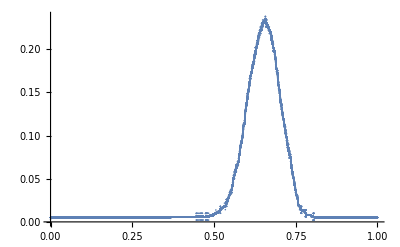

```mathematica
ListPlot[filedata12, PlotRange->All]
```

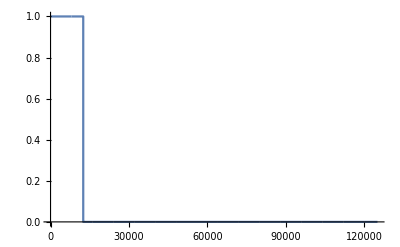

```mathematica
pulse = Table[If[n>Length[filedata]/10,0,1],{n,Length[filedata]}];
ListPlot[pulse, PlotRange->All,Joined->True]
```

```mathematica
filedataft = Fourier[filedata2];
pulseft = Fourier[pulse];
```

```mathematica
ListPlot[{Re[filedataft],Im[filedataft],Re[pulseft],Im[pulseft]}, PlotRange->{{0,100},All}, Joined->True]
```

-Graphics-

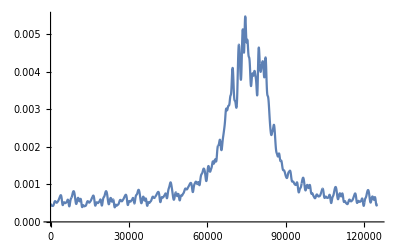

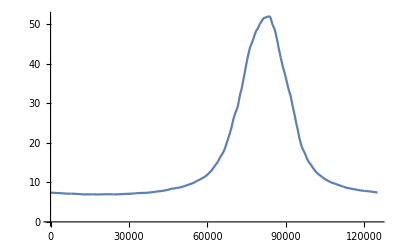

Part::partw: Part 2 of Fourier[{}] does not exist.

Part::partw: Part 3 of Fourier[{}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

InverseFourier::fftl: Argument (If[Abs[Fourier[{}]⟦2⟧] < 0.1`, 10, FractionBox[1, pulseft⟦n⟧]]\ Fourier[{}]⟦2⟧)/ⅇ^(1/2500)(If[Abs[Fourier[{}]⟦3⟧] < 0.1`, 10, FractionBox[1, pulseft⟦n⟧]]\ Fourier[{}]⟦3⟧)/ⅇ^(9/10000)(If[Abs[Fourier[{}]⟦4⟧] < 0.1`, 10, FractionBox[1, pulseft⟦n⟧]]\ Fourier[{}]⟦4⟧)/ⅇ^(1/625)(If[Abs[Fourier[{}]⟦5⟧] < 0.1`, 10, FractionBox[1, pulseft⟦n⟧]]\ Fourier[{}]⟦5⟧)/ⅇ^(1/400)41(If[Abs[Fourier[{}]⟦47⟧] < 0.1`, 10, FractionBox[1, pulseft⟦n⟧]]\ Fourier[{}]⟦47⟧)/ⅇ^(2209/10000)(If[Abs[Fourier[{}]⟦48⟧] < 0.1`, 10, FractionBox[1, pulseft⟦n⟧]]\ Fourier[{}]⟦48⟧)/ⅇ^(144/625)(If[Abs[Fourier[{}]⟦49⟧] < 0.1`, 10, FractionBox[1, pulseft⟦n⟧]]\ Fourier[{}]⟦49⟧)/ⅇ^(2401/10000)(If[Abs[Fourier[{}]⟦50⟧] < 0.1`, 10, FractionBox[1, pulseft⟦n⟧]]\ Fourier[{}]⟦50⟧)/ⅇ^(1/4)124950 is not a non-empty list or rectangular array of numeric quantities. ButtonBox["»",
Appearance->{Automatic, None},
BaseStyle->"Link",
ButtonData:>"paclet:ref/message/InverseFourier/fftl",
ButtonNote->"InverseFourier::fftl"]

InverseFourier::fftl: Argument {{},0.9996000799893344 If[Abs[Fourier[{}]⟦2⟧]<0.1,10.,1./pulseft⟦n⟧] Fourier[{}]⟦2⟧,0.9991004048785273 If[Abs[Fourier[{}]⟦3⟧]<0.1,10.,1./pulseft⟦n⟧] Fourier[{}]⟦3⟧,0.9984012793176063 If[Abs[Fourier[{}]⟦4⟧]<0.1,10.,1./pulseft⟦n⟧] Fourier[{}]⟦4⟧,«44»,0.786549202213455 If[Abs[Fourier[{}]⟦49⟧]<0.1,10.,1./pulseft⟦n⟧] Fourier[{}]⟦49⟧,0.7788007830714049 If[Abs[Fourier[{}]⟦50⟧]<0.1,10.,1./pulseft⟦n⟧] Fourier[{}]⟦50⟧,«124950»} is not a non-empty list or rectangular array of numeric quantities.

InverseFourier::fftl: Argument {{},0.9996 If[Abs[Fourier[{}]⟦2⟧]<0.1,10.,1./pulseft⟦n⟧] Fourier[{}]⟦2⟧,0.9991 If[Abs[Fourier[{}]⟦3⟧]<0.1,10.,1./pulseft⟦n⟧] Fourier[{}]⟦3⟧,0.998401 If[Abs[Fourier[{}]⟦4⟧]<0.1,10.,1./pulseft⟦n⟧] Fourier[{}]⟦4⟧,0.997503 If[Abs[Fourier[{}]⟦5⟧]<0.1,10.,1./pulseft⟦n⟧] Fourier[{}]⟦5⟧,«42»,0.794216 If[Abs[Fourier[{}]⟦48⟧]<0.1,10.,1./pulseft⟦n⟧] Fourier[{}]⟦48⟧,0.786549 If[Abs[Fourier[{}]⟦49⟧]<0.1,10.,1./pulseft⟦n⟧] Fourier[{}]⟦49⟧,0.778801 If[Abs[Fourier[{}]⟦50⟧]<0.1,10.,1./pulseft⟦n⟧] Fourier[{}]⟦50⟧,«124950»} is not a non-empty list or rectangular array of numeric quantities.

ListPlot::lpn: Abs[InverseFourier[{{},0.9996 If[Abs[Part[«2»]]<0.1,10.,1./Part[«2»]] Fourier[{}]⟦2⟧,0.9991 If[Abs[Part[«2»]]<0.1,10.,1./Part[«2»]] Fourier[{}]⟦3⟧,0.998401 If[Abs[Part[«2»]]<0.1,10.,1./Part[«2»]] Fourier[{}]⟦4⟧,0.997503 If[Abs[Part[«2»]]<0.1,10.,1./Part[«2»]] Fourier[{}]⟦5⟧,«42»,0.794216 If[Abs[Part[«2»]]<0.1,10.,1./Part[«2»]] Fourier[{}]⟦48⟧,0.786549 If[Abs[Part[«2»]]<0.1,10.,1./Part[«2»]] Fourier[{}]⟦49⟧,0.778801 If[Abs[Part[«2»]]<0.1,10.,1./Part[«2»]] Fourier[{}]⟦50⟧,«124950»}]] is not a list of numbers or pairs of numbers.

InverseFourier::fftl: Argument {{},0.9996000799893344 If[Abs[Fourier[{}]⟦2⟧]<0.1,10.,1./pulseft⟦n⟧] Fourier[{}]⟦2⟧,0.9991004048785273 If[Abs[Fourier[{}]⟦3⟧]<0.1,10.,1./pulseft⟦n⟧] Fourier[{}]⟦3⟧,0.9984012793176063 If[Abs[Fourier[{}]⟦4⟧]<0.1,10.,1./pulseft⟦n⟧] Fourier[{}]⟦4⟧,«44»,0.786549202213455 If[Abs[Fourier[{}]⟦49⟧]<0.1,10.,1./pulseft⟦n⟧] Fourier[{}]⟦49⟧,0.7788007830714049 If[Abs[Fourier[{}]⟦50⟧]<0.1,10.,1./pulseft⟦n⟧] Fourier[{}]⟦50⟧,«124950»} is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of InverseFourier::fftl will be suppressed during this calculation.

ListPlot::lpn: Abs[InverseFourier[{{},0.9996 If[Abs[Part[«2»]]<0.1,10.,1./Part[«2»]] Fourier[{}]⟦2⟧,0.9991 If[Abs[Part[«2»]]<0.1,10.,1./Part[«2»]] Fourier[{}]⟦3⟧,0.998401 If[Abs[Part[«2»]]<0.1,10.,1./Part[«2»]] Fourier[{}]⟦4⟧,0.997503 If[Abs[Part[«2»]]<0.1,10.,1./Part[«2»]] Fourier[{}]⟦5⟧,«42»,0.794216 If[Abs[Part[«2»]]<0.1,10.,1./Part[«2»]] Fourier[{}]⟦48⟧,0.786549 If[Abs[Part[«2»]]<0.1,10.,1./Part[«2»]] Fourier[{}]⟦49⟧,0.778801 If[Abs[Part[«2»]]<0.1,10.,1./Part[«2»]] Fourier[{}]⟦50⟧,«124950»}]] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[Abs[InverseFourier[{{},(If[Abs[Fourier[{}]⟦2⟧]<0.1,10,1/pulseft⟦n⟧] Fourier[{}]⟦2⟧)/ⅇ^(1/2500),(If[Abs[Fourier[{}]⟦3⟧]<0.1,10,1/pulseft⟦n⟧] Fourier[{}]⟦3⟧)/ⅇ^(9/10000),(If[Abs[Fourier[{}]⟦4⟧]<0.1,10,1/pulseft⟦n⟧] Fourier[{}]⟦4⟧)/ⅇ^(1/625),124993,(If[Abs[Fourier[{}]⟦124998⟧]<0.1,10,1/pulseft⟦n⟧] Fourier[{}]⟦124998⟧)/ⅇ^(3906125001/2500),(If[Abs[Fourier[{}]⟦124999⟧]<0.1,10,1/pulseft⟦n⟧] Fourier[{}]⟦124999⟧)/ⅇ^(15624750001/10000),(If[Abs[Fourier[{}]⟦125000⟧]<0.1,10,1/pulseft⟦n⟧] Fourier[{}]⟦125000⟧)/ⅇ^1562500}]],PlotRange→All,Joined→True]
 |  |  |  |

ListConvolve::kldims: The kernel … and list {} are not both non-empty lists with the same tensor rank.

InverseFourier::fftl: Argument {{},0.9996000799893344 If[Abs[Fourier[{}]⟦2⟧]<0.1,10.,1./pulseft⟦n⟧] Fourier[{}]⟦2⟧,0.9991004048785273 If[Abs[Fourier[{}]⟦3⟧]<0.1,10.,1./pulseft⟦n⟧] Fourier[{}]⟦3⟧,0.9984012793176063 If[Abs[Fourier[{}]⟦4⟧]<0.1,10.,1./pulseft⟦n⟧] Fourier[{}]⟦4⟧,«44»,0.786549202213455 If[Abs[Fourier[{}]⟦49⟧]<0.1,10.,1./pulseft⟦n⟧] Fourier[{}]⟦49⟧,0.7788007830714049 If[Abs[Fourier[{}]⟦50⟧]<0.1,10.,1./pulseft⟦n⟧] Fourier[{}]⟦50⟧,«124950»} is not a non-empty list or rectangular array of numeric quantities.

ListConvolve::kldims: The kernel Abs[InverseFourier[{{},0.9996000799893344 If[Abs[Part[«2»]]<0.1,10.,1./Part[«2»]] Fourier[{}]⟦2⟧,0.9991004048785273 If[Abs[Part[«2»]]<0.1,10.,1./Part[«2»]] Fourier[{}]⟦3⟧,0.9984012793176063 If[Abs[Part[«2»]]<0.1,10.,1./Part[«2»]] Fourier[{}]⟦4⟧,«44»,0.786549202213455 If[Abs[Part[«2»]]<0.1,10.,1./Part[«2»]] Fourier[{}]⟦49⟧,0.7788007830714049 If[Abs[Part[«2»]]<0.1,10.,1./Part[«2»]] Fourier[{}]⟦50⟧,«124950»}]] and list {} are not both non-empty lists with the same tensor rank.

InverseFourier::fftl: Argument {{},0.9996 If[Abs[Fourier[{}]⟦2⟧]<0.1,10.,1./pulseft⟦n⟧] Fourier[{}]⟦2⟧,0.9991 If[Abs[Fourier[{}]⟦3⟧]<0.1,10.,1./pulseft⟦n⟧] Fourier[{}]⟦3⟧,0.998401 If[Abs[Fourier[{}]⟦4⟧]<0.1,10.,1./pulseft⟦n⟧] Fourier[{}]⟦4⟧,0.997503 If[Abs[Fourier[{}]⟦5⟧]<0.1,10.,1./pulseft⟦n⟧] Fourier[{}]⟦5⟧,«42»,0.794216 If[Abs[Fourier[{}]⟦48⟧]<0.1,10.,1./pulseft⟦n⟧] Fourier[{}]⟦48⟧,0.786549 If[Abs[Fourier[{}]⟦49⟧]<0.1,10.,1./pulseft⟦n⟧] Fourier[{}]⟦49⟧,0.778801 If[Abs[Fourier[{}]⟦50⟧]<0.1,10.,1./pulseft⟦n⟧] Fourier[{}]⟦50⟧,«124950»} is not a non-empty list or rectangular array of numeric quantities.

ListConvolve::kldims: The kernel Abs[InverseFourier[{{},0.9996 If[Abs[Part[«2»]]<0.1,10.,1./Part[«2»]] Fourier[{}]⟦2⟧,0.9991 If[Abs[Part[«2»]]<0.1,10.,1./Part[«2»]] Fourier[{}]⟦3⟧,0.998401 If[Abs[Part[«2»]]<0.1,10.,1./Part[«2»]] Fourier[{}]⟦4⟧,0.997503 If[Abs[Part[«2»]]<0.1,10.,1./Part[«2»]] Fourier[{}]⟦5⟧,«42»,0.794216 If[Abs[Part[«2»]]<0.1,10.,1./Part[«2»]] Fourier[{}]⟦48⟧,0.786549 If[Abs[Part[«2»]]<0.1,10.,1./Part[«2»]] Fourier[{}]⟦49⟧,0.778801 If[Abs[Part[«2»]]<0.1,10.,1./Part[«2»]] Fourier[{}]⟦50⟧,«124950»}]] and list {} are not both non-empty lists with the same tensor rank.

General::stop: Further output of ListConvolve::kldims will be suppressed during this calculation.

```mathematica
deconv = InverseFourier[Table[filedataft[[n]]Exp[-((n/100)^2)]If[Abs[pulseft[[n]]]<0.1,10,1/pulseft[[n]]], {n,125000}]];
ListPlot[Abs[deconv], PlotRange->All,Joined->True]
ListPlot[ListConvolve[Abs[deconv],pulse,1], Joined->True]
```